```mathematica
(* Explicit Euiler*)
logisticIC=0.01;
logisticExact[t_]:=0.01 / (0.01 + 0.99 * E^(-10 *t));
errorListPlot[approx_]:=(
ListPlot[Table[{approx[[i,1]],Abs[logisticExact[approx[[i,1]]]-approx[[i,2]]]},{i,1,Length[approx]}]]
);
```

```mathematica
ExplicitEuiler[f_,ic_,h_,T_] := (
Block[{sol,n,i},
n = T / dt;
sol = Table[0,{n+1}];
sol[[1]] = ic;
For[i=1,i<=n,++i,
sol[[i+1]] = sol[[i]] + h *10 sol[[i]](1-sol[[i]]);
];
{sol,Table[{(i-1)h,sol[[i]]},{i,1,Length[sol]}]}
]
);
Print[N[logisticExact[5]]];
logisticExact[t_] := 0.01 / (0.01 + 0.99 * E^(-10 *t));

Print[N[f[25]]];
```

1.

1.

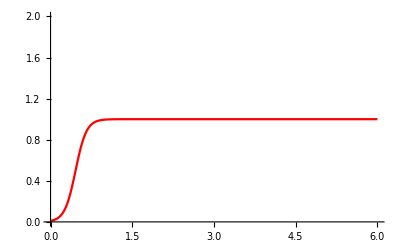

```mathematica
Plot[logisticExact[t],{t,0,6},PlotRange->{{0,6},{0,2}},PlotStyle->Red]
```